## Efficient Eigenbasis Generation

```mathematica
(* TODO: inf square well *)
(* TODO: quantum harmonic oscillator *)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
(* no normalisation *)
```

```mathematica
eigenvalue[n_] = (n + 1/2) ;
eigenfunction[n_, r_] = 2^(-n/2) Exp[-r^2/2] HermiteH[n,r];
eigenfunction[n_, r_, t_] = Exp[ - ⅈ t eigenvalue[n]] eigenfunction[n, r];
```

# Intro

introduce complex wavefunction

```mathematica
normalise[f_, r_] := f/(√Integrate[ Abs[f /. r -> r1]^2, {r1, -∞, ∞}])   (* NO NEED TO PUT HERE *)
```

```mathematica
exampleψ[x_] =  (ⅇ^(-(-1+x)^4-2 ⅈ π x)+(ⅇ^(-ⅈ ⅇ^(-x^2)-(x-2)^2/2))/π^(1/4))2/3
```

2/3 (ⅇ^(-(-1+x)^4-2 ⅈ π x)+(ⅇ^(-ⅈ ⅇ^(-x^2)-1/2 (-2+x)^2))/π^(1/4))

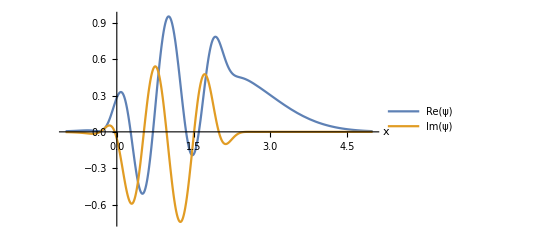

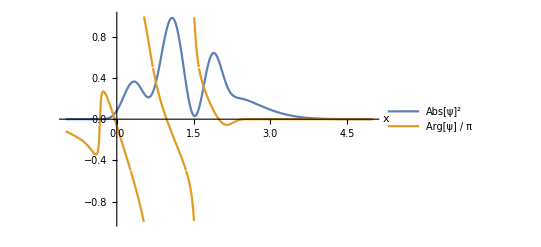

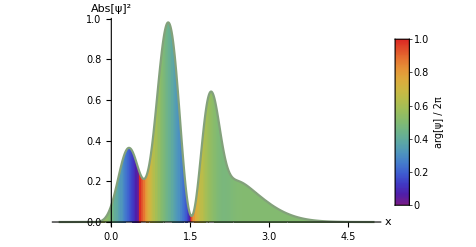

```mathematica
domain = {x, -1, 5};
Plot[
	{Re[exampleψ[x]], Im[exampleψ[x]]}, domain,
	AxesLabel-> {x}, PlotRange -> All,
	PlotLegends-> {Re[ψ], Im[ψ]}
]

Plot[
	{Abs[exampleψ[x]]^2, Arg[exampleψ[x]]/(π)}, domain,
	AxesLabel-> {x}, PlotRange-> All,
	PlotLegends-> {Abs[ψ]^2, "Arg[ψ] / π"}
]

plotWavefunction[psi_, {r_, range__}, showbar_] :=
	Plot[
		Abs[psi]^2, {r, range}, 
		AxesLabel -> {r, Abs[ψ]^2},
		PlotRange -> All,
		ColorFunction -> (ColorData["Rainbow"][Rescale[Arg[psi /. r -> #], {-π, π}]] &),
		ColorFunctionScaling -> False,
		Filling -> Axis,
		PlotLegends -> If[showbar == True, BarLegend["Rainbow", LegendLabel -> "arg[ψ] / 2π"], None]
	]
plotWavefunction[psi_, domain_] :=
	plotWavefunction[psi, domain, True]
	
plotWavefunction[exampleψ[x], domain]


exampleψ[space_, time_] =
	NDSolveValue[
		{ⅈ Derivative[0,1][ψ][x,t] == Derivative[2,0][ψ][x, t] / 2,
		 ψ[x, 0] == exampleψ[x]},
		 ψ, {x, -2, 8}, {t, 0, 0.3}
	][space, time];

animateWavefunction[psi_, domain_, {t1_, times__}] :=
	Animate[
		plotWavefunction[psi /. t1 -> t, domain, False],
		{t, times}
	]

animateWavefunction[
	exampleψ[x, t],
	domain,
	{t, 0, 0.3}
]
```

```mathematica
Animate[
	Overlay[
		{Show[
			plotWavefunction[exampleψ[x, t], domain, False],
			Plot[Abs[exampleψ[x, t]]^2,
				{x, 2, 3}, Filling -> Axis,
				PlotRange -> {0, 1.2},
				PlotStyle -> Red]],
		 Text[
			Style[
				"Pr(2 < x < 3) \n= " <>
				ToString[NIntegrate[Abs[exampleψ[x, t]]^2, {x, 2, 3}]], 
				Red]]	},
		Alignment->{0.8, 0}],
	{t, 0, 0.3}
]
```

```mathematica
Animate[
	Overlay[{
		Show[
			Histogram[samples[[;;n]], {0.1}, "ProbabilityDensity"],
			Plot[
				{Abs[exampleψ[x]]^2, 
				 ConditionalExpression[Abs[exampleψ[x]]^2, x > 2 && x < 3]},
				 domain, Filling-> Axis, PlotStyle->{Default, Red}],
			AxesLabel -> {"x", Abs[ψ]^2}, PlotRange -> {0, 1}
		],
		Text[
			"# measurements ∈ [2, 3] \n=" <>
			StringTake[ToString[
				N[Count[samples[[;;n]], u_ /; u > 2 && u < 3] / 
				  If[n > 0, n, 1]]
			], UpTo[4]] <> "%"]},
		Alignment -> {1, 0}],
	{{n, 0, "# measurements"}, 0, Length[samples], 1}
]
```

```mathematica
Count[{1, 2, 3, 4},x_/;x>5]
```

0

```mathematica
∈
```

```mathematica
ConditionalExpression[x > 2, x^2]
```

```mathematica
Condition
```

```mathematica
Count[{1, 2, 3, 4, 9},x_/;x>5]
```

1

```mathematica
"12345"[[3]]
```

Part::partd: Part specification 12345⟦3⟧ is longer than depth of object.

12345⟦3⟧